```mathematica
g=15-x;
a=0;
b=15;
A=Integrate[g,{x,a,b}];
k=1/A
f=k g;(* THIS IS THE PDF.  USE THIS FOR EVERYTHING BELOW*)
Integrate[f,{x,a,b}]
EV=Integrate[x f,{x,a,b}]
Var=Integrate[(x-EV)^2 f,{x,a,b}]
```

2/225

1

5

25/2

```mathematica
(*P(X<=1),P(X<=2),F=P(X<=x)*)
Integrate[ f,{x,a,1}]
Integrate[ f,{x,a,2}]
F=Integrate[ f,{x,a,x}]
```

29/225

56/225

(2 x)/15-x^2/225

```mathematica
Solve[(2 x)/15-x^2/225==0.6,x,Reals]
```

{{x→5.51317},{x→24.4868}}

```mathematica
Solve[(2 x)/15-x^2/225==0.95,x,Reals]
```

{{x→11.6459},{x→18.3541}}

```mathematica
Solve[F==0.6]
```

{{x→5.51317},{x→24.4868}}

```mathematica
Solve[1-1/x==0.9]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→10.}}

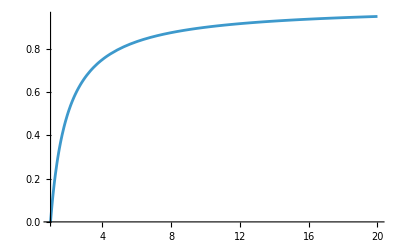

```mathematica
Plot[1-1/x,{x,1,20},PlotRange->All]
```

```mathematica
Solve[1-Exp[-x λ]==0.5,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.693147/λ}}

```mathematica
Solve[Integrate[64/(x+2)^5,{x,0,xp}]==0.6,xp,Reals]
Solve[Integrate[64/(x+2)^5,{x,0,xp}]==0.07,xp,Reals]
Solve[Integrate[64/(x+2)^5,{x,0,xp}]==0.99,xp,Reals]
```

{{xp→0.514867}}

{{xp→0.0366165}}

{{xp→4.32456}}

```mathematica
Solve[Integrate[1/Sqrt[37.5352*π]*Exp[-(1/37.5352)*(x-3.2)^2],{x,-Infinity,xp}]==0.6,xp,Reals]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

```mathematica
NSolve[Integrate[1/Sqrt[37.5352*π]*Exp[-(1/37.5352)*(x-3.2)^2],{x,-Infinity,xp}]==0.6,xp,Reals]
```

{{xp→4.29754}}

```mathematica
NSolve[Integrate[1/Sqrt[37.5352*π]*Exp[-(1/37.5352)*(x-3.2)^2],{x,-Infinity,xp}]==0.99,xp,Reals]
```

{{xp→13.2781}}

```mathematica
μ=21
σ=5
f=1/Sqrt[2 Pi σ^2] Exp[-1/2 ((x-μ)/σ)^2]
a=-Infinity
b=Infinity
Integrate[f,{x,a,b}]
NIntegrate[f,{x,a,22}]
```

21

5

(ⅇ^(-1/50 (-21+x)^2))/(5 √(2 π))

-∞

∞

1

0.57926